## functions

### misc. functions and styles used throughout

```mathematica
Import["~/Code/cytomod/analysis/cytomod_functions.m"];
```

```mathematica
meanorzero[x_]:=If[Length[x]>0,Mean[x],0];
errorzero[x_]:=If[Length[x]>1,StandardDeviation[x]/Sqrt[Length[x]],0];

doublyBound[m_]:=Cases[m,_?((#[[5]]!=-1&&#[[6]]!=-1)&),1,Heads->False];
divorzero[x_,y_]:=If[y≠0,x/y,0];
myrijP[x_,zpos_,fov_]:=Join[rijP[x[[1;;2]]-zpos[[1;;2]],fov],x[[3;;]]];
constFun[l_,x_]:={l,ConstantArray[x,Length[l]]}ᵀ;
riffleNones[l_]:=Riffle[Riffle[l,None],None,3];

fs=Directive[Opacity[1],Thickness[0.01]];
forestgreen=RGBColor[34/255,139/255,34/255];
skyblue=RGBColor[135/255,206/255,250/255];
cols={Red,Darker[Cyan]};
c1[x_]:=Style[ToString[x],cols[[1]]];
c2[x_]:=Style[ToString[x],cols[[2]]];
vline[th_]:=Graphics[{Thickness[th],Line[{{0,-1},{0,1}}]}];
```

### functions for drawing lattices

```mathematica
latticeFromDomain[x_,ll_:0.037,lf_:25]:=If[Length[x]>0,Round[Range[x[[1]],x[[-1]],ll]/ll],Nothing];

fullLatFromAllDomains[doms1_,doms2_,lf_:25,lb_:0.037]:=Module[{},
x=ConstantArray[0,Ceiling[lf/lb]];
x[[Flatten[doms1]+1]]=1;
x[[Flatten[doms2]+1]]=2;
x
];

fullLatFromManyDomains[domsarr_,lf_:25,lb_:0.037]:=Module[{},
x=ConstantArray[0,Ceiling[lf/lb]];
Do[x[[Flatten[domsarr[[i]]]+1]]=i,{i,Length[domsarr]}];
x
];
```

### filenames and directories

```mathematica
headdir=outdir<>"/xlink_segregation/spacers";
headdirL=outdir<>"/xlink_segregation/lattice";
figdir=outdir<>"/xlink_segregation/figs/paper";

doms={"1","2"};
domfs="/analysis/spacer"<>ToString[#]<>"_domains_t1-2000_nc4_rc1.dat"&/@doms;
domfsf0="/analysis/spacer"<>ToString[#]<>"_domains_f0_t1-2000_nc4_rc1.dat"&/@doms;
angf="/analysis/ang_bw_fils.dat";
```

### calclulating gap lengths

```mathematica
gaplengths[s1doms_,s2doms_]:=Module[{},
If[
Length[s1doms]==0||Length[s2doms]==0,
gls={},
domeps=Join[s1doms[[All,1]],s1doms[[All,2]],s2doms[[All,1]],s2doms[[All,2]]];
domeplabs= Join[ConstantArray[1,2*Length[s1doms]],ConstantArray[2,2*Length[s2doms]]];
sort=Ordering[domeps];
gapPoss=Flatten[Position[Differences[domeplabs[[sort]]],_?((#≠0)&)]];
gls=Differences[domeps[[sort]]][[gapPoss]]
];
gls
];
```

## fig 1 : afines can make domains

```mathematica
s1denss={0.1,0.124,0.167,0.201,0.222,0.250,0.273,0.300,0.333,0.375,0.400};
denstot=0.5;
s2denss=denstot-s1denss;
densrats=s1denss/s2denss;
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/denstot_",denstot,"_s2init/seed3e7/lgrow0_s1dens",dens
}],{dens,s1densstrs}];
densratstrs=ToString[NumberForm[#,{2,2}]]&/@densrats;
t=500;
```

### movies

```mathematica
idxs={4,6,9};
s1denss[[idxs]]/s2denss[[idxs]]
```

```mathematica
links=pts4[#,"links"]&/@(dirs[[idxs]]);
conn1s=pts4[#,"spacers1_bound"]&/@(dirs[[idxs]]);
conn2s=pts4[#,"spacers2_bound"]&/@(dirs[[idxs]]);
```

```mathematica
myrijP[x_,zpos_,fov_]:=Join[rijP[x[[1;;2]]-zpos[[1;;2]],fov],x[[3;;]]];
```

```mathematica
linkz=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];
```

```mathematica
mov=Table[drawmixed[{},linkz[[i]],conn1z[[i]],conn2z[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];
```

```mathematica
trimovie=Table[GraphicsRow[{mov[[1,t]],mov[[2,t]],mov[[3,t]]},Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
```

```mathematica
Export[figdir<>"/diff100_denstot0.5_t500_frames/densrats0-67_1_2.avi",trimovie];
```

### frames

```mathematica
t=500;
links=pts4[#,"links"][[t]]&/@dirs;
```

```mathematica
conn1s=doublyBound[pts4[#,"spacers1_bound"][[t]]]&/@dirs;
conn2s=doublyBound[pts4[#,"spacers2_bound"][[t]]]&/@dirs;
```

$Aborted

$Aborted

```mathematica
frs1=drawmixed[{},links,conn1s,conn2s,"",False,{35,20},False,26,Green,Red,Darker[Cyan]];
```

```mathematica
Do[Export[figdir<>"/diff100_denstot0.5_t500_frames/densrat"<>densratstrs[[i]]<>".eps",frs1[[i]]],{i,Length@densrats}];
```

### domain calculation

```mathematica
dom1s=Map[ToExpression,importCheck[#<>domfs[[1]]]&/@dirs,{3}][[All,t]];
dom2s=Map[ToExpression,importCheck[#<>domfs[[2]]]&/@dirs,{3}][[All,t]];
```

```mathematica
latdoms1=Map[latticeFromDomain,dom1s[[All,1]],{2}];
latdoms2=Map[latticeFromDomain,dom2s[[All,1]],{2}];
```

```mathematica
latsT=Table[fullLatFromAllDomains[latdoms1[[i]],latdoms2[[i]]],{i,Length[densrats]}];
```

```mathematica
lattices=Import[#<>"/lattice.dat","CSV"][[-1]]&/@dirs;
```

```mathematica
lattices2=Table[lattice/.{1->4,2->5},{lattice,lattices}];
lattices3=lattices2+latsT[[All,1;;Dimensions[lattices][[2]]]];
```

```mathematica
maxl=15;
```

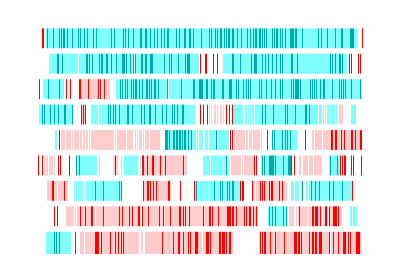

```mathematica
p1=ArrayPlot[lattices3[[2;;-2]],AspectRatio->0.7,FrameLabel->{"ρ_short/ρ_long","position (μm)"},DataRange->{{0,maxl},{1,Length[densrats]-2}},BaseStyle->Directive[FontSize->22,FontColor->Blue],
(*ColorRules->{5->Black,7->Green,1->Gray,2->(*Darker[Green]*)forestgreen,0->White},*)
ColorRules->{5->Red,7->Darker[Cyan],1->Blend[{Red,White},0.8],2->Blend[{Cyan,White},0.5],0->White,4->White,6->White},
BaseStyle->{FontFamily->"Arial",FontSize->22,SingleLetterItalics->False},FrameStyle->Black,FrameTicks->{{Range[Length[densrats]-2,1,-1],densratstrs[[2;;-2]]}ᵀ,Range[0,25,5]},GridLines->{None,Range[1,Length[densrats]-1]+0.5},GridLinesStyle->Directive[White,Thickness[0.01]],Method->{"GridLinesInFront"->True}]
```

```mathematica
{{Export[figdir<>"/domains_and_spacers_vs_densrat_ldiff100_lgrow0_denstot0.5.eps",p1];}, {Export[figdir<>"/domains_and_spacers_vs_densrat_ldiff100_lgrow0_denstot0.5.png",p1];}}
```

{{Null},{Null}}

## fig 2 : simulation and lattice for mechanical constraints (dx and lp)

```mathematica
s1domfL="/analysis/spacer1_domains_t9000-10000_nc4_rc1.dat";
s2domfL="/analysis/spacer2_domains_t9000-10000_nc4_rc1.dat";
winlenL=10000-9000;
domfsL={s1domfL,s2domfL};
doms={1,2};
```

### lgrow = 0, dx varying

```mathematica
dxs={"0.000","0.010","0.027","0.05","0.1","0.2","0.5","1"};
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
ti=1;(*350;*)(*1000;*)
angThresh=0.8;
winlen=1999;

avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/avg_err_ns_ti1_wl1999 already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999 already exists.

```mathematica
ParallelDo[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/s1len0.20_ldiff",ld,"_s1dens",s1dens}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"ldiff",ld,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{ld,dxs}
];
```

```mathematica
Do[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/s1len0.20_ldiff",ld,"_s1dens",s1dens}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[1]]]&,dirs,{1}];
s2doms=Map[importCheck[#<>domfs[[2]]]&,dirs,{1}];
glsST=Table[gaplengths[s1doms[[i,t,1]],s2doms[[i,t,1]]],{i,Length[s1doms]},{t,Length[s1doms[[i]]]}];

fname=StringJoin[ToString/@{"ldiff",ld,"_gap_lengths.dat"}];
dirsuf="/";

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,glsST,{2}],"Table"];,

{ld,dxs}
];
```

lattice

```mathematica
job="len15_lp17.000_mu2-0.008_munn0.000";
topdirL=headdirL<>"/"<>job;
seeds=Range[20];
mu1="-0.00800";
ti=1;
```

```mathematica
Do[
dirs=Table[StringJoin[ToString/@{topdirL,"/seed",sd,"e6/lendiff",ld,"_mu1",mu1}],{sd,seeds}];

s1doms=Map[importCheck[#<>domfsL[[ndom]]]&,dirs,{1}];
fname=StringJoin[ToString/@{"ldiff",ld,"_doms",ndom,".dat"}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlenL}];

outf=topdirL<>"/dom_lens/t100_window"<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];

outf=topdirL<>"/dom_lens/avg_err_ns"<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{ndom,doms},
{ld,dxs}
];
```

### importing

afines

```mathematica
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensA=errcurves[ToExpression/@dxs,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

lattice

```mathematica
job="len15_lp17.000_mu2-0.008_munn0.000";
topdirL=headdirL<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdirL,"/dom_lens/avg_err_ns/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensL=errcurves[ToExpression/@dxs,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

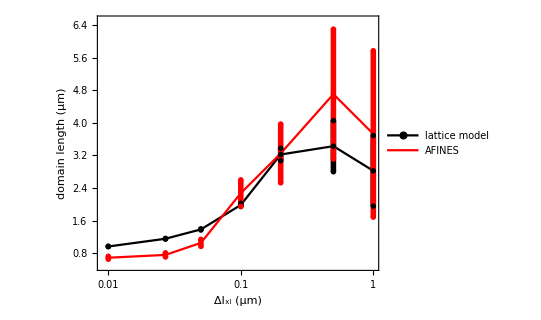

```mathematica
curves=Join[domlensL,domlensA];
cols={Black,Red};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}]
];
labels={"lattice model","AFINES"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->{Automatic,{0.5,6.5}},
FrameLabel->{"Δl_xl (μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[{1,4}]]],Spacings->0],{0.35,0.75}]]
```

```mathematica
Export[figdir<>"/mar19/dxl_lgrow0_both.eps",p1];
```

#### gap lengths

```mathematica
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1_wl1999/ldiff",dx,"_gap_lengths.dat"}],{dx,dxs}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
```

```mathematica
dps
```

{/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.000_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.010_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.027_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.05_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.1_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.2_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff0.5_gap_lengths.dat,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_lgrow0_len15/dom_lens/ti1_wl1999/ldiff1_gap_lengths.dat}

```mathematica
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensA=errcurves[ToExpression/@dxs,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

#### drawing

```mathematica
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
dirs=Table[StringJoin[ToString/@{topdir,"/seed1e7/s1len0.20_ldiff",dx,"_s1dens0.250"}],{dx,dxs}];
```

```mathematica
links=pts4[#,"links"][[1001;;1100]]&/@dirs;
```

```mathematica
conn1s=pts4[#,"spacers1_bound"][[1001;;1100]]&/@dirs;
conn2s=pts4[#,"spacers2_bound"][[1001;;1100]]&/@dirs;
```

```mathematica
frs1=drawmixed[{},links[[All,-1]],conn1s[[All,-1]],conn2s[[All,-1]],"",False,{35,20},False,1,Green,cols[[1]],cols[[2]]];
```

```mathematica
Do[Export[figdir<>"/mar19/dx"<>dxs[[i]]<>"_t1100.eps",frs1[[i]]],{i,Length[dxs]}]
```

### lgrow = 0, lp varying

```mathematica
lkbs={"0.01","0.03","0.05","0.068","0.10","0.15","0.20","0.25","0.30","0.50"};
lps=ToExpression/@lkbs/0.004;
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="lkb_grow0_s2dens0.25_ldiff0.100";
topdir=headdir<>"/"<>job;
ti=1;
angThresh=0.8;
winlen=1999;
s1dens="0.250";

avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

```mathematica
ParallelDo[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/lkb",lkb,"_s1dens",s1dens}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"lkb",lkb,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{lkb,lkbs}
];
```

lattice

```mathematica
job="len15_diff0.1_mu2-0.008_muC0.000";
topdirL=headdirL<>"/"<>job;
seeds=Range[20];
mu1="-0.00800";
ti=1;
```

```mathematica
Do[
dirs=Table[StringJoin[ToString/@{topdirL,"/seed",sd,"e6/lkb",lkb,"_mu1",mu1}],{sd,seeds}];

fname=StringJoin[ToString/@{"lkb",lkb,"_doms",ndom,".dat"}];
s1doms=Map[importCheck[#<>domfsL[[ndom]]]&,dirs,{1}];

s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlenL}];

outf=topdirL<>"/dom_lens/t100_window"<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];

outf=topdirL<>"/dom_lens/avg_err_ns"<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{ndom,doms},
{lkb,lkbs}
];
```

### importing

afines

```mathematica
job="lkb_grow0_s2dens0.25_ldiff0.100";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensA=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

lattice

```mathematica
job="len15_diff0.1_mu2-0.008_muC0.000";
topdirL=headdirL<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdirL,"/dom_lens/avg_err_ns/lkb",dx,"_doms",dom,".dat"}],{dx,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensL=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

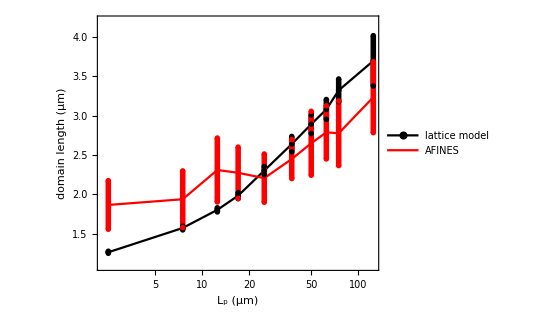

```mathematica
curves=Join[domlensL,domlensA];
cols={Black,Red};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}]
];
labels={"lattice model","AFINES"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->{Automatic,{1.1,4.2}},
FrameLabel->{"L_p (μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[{1,4}]]],Spacings->0],{0.35,0.75}]]
```

```mathematica
Export[figdir<>"/mar19/lp_lgrow0_both.eps",p1];
```

### lgrow = 40, dx varying

```mathematica
dxs={"0.000","0.010","0.027","0.05","0.1","0.2","0.5","1"};
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="ldiff_lgrow0.040";
topdir=headdir<>"/"<>job;
ti=1;
angThresh=0.8;
winlen=1999;
```

```mathematica
avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

```mathematica
ParallelDo[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/s1len0.20_ldiff",ld}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"ldiff",ld,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{ld,dxs}
];
```

### importing

afines growing

```mathematica
job="ldiff_lgrow0.040";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns_ti350/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensG=errcurves[ToExpression/@dxs,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

afines non-growing

```mathematica
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns_ti1/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensNG=errcurves[ToExpression/@dxs,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

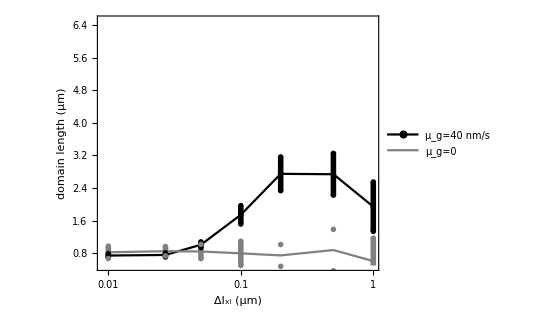

```mathematica
curves=Join[domlensG,domlensNG];
cols={Black,Gray};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}]
];
labels={"μ_g=40 nm/s","μ_g=0"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->{Automatic,{0.5,6.5}},
FrameLabel->{"Δl_xl (μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[{1,4}]]],Spacings->0],{0.35,0.75}]]
```

```mathematica
Export[figdir<>"/dxl_difft_mug_g_ti350_vs_ng_ti1.eps",p1];
```

### lgrow = 40, lp varying

```mathematica
lkbs={"0.01","0.03","0.05","0.068","0.10","0.15","0.20","0.25","0.30","0.50"};
lps=ToExpression/@lkbs/0.004;
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="lp_lgrow0.040";
topdir=headdir<>"/"<>job;
ti=1;
angThresh=0.8;
winlen=1999;
s1dens="0.250";

avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

```mathematica
Do[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/lkb",lkb}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"lkb",lkb,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{lkb,lkbs}
];
```

### importing

afines non growing

```mathematica
job="lkb_grow0_s2dens0.25_ldiff0.100";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns_ti350/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensNG=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

afines growin

```mathematica
job="lp_lgrow0.040";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/avg_err_ns_ti350/lkb",dx,"_doms",dom,".dat"}],{dx,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensG=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

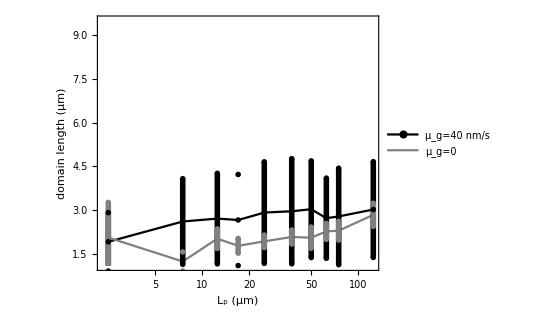

```mathematica
curves=Join[domlensG,domlensNG];
cols={Black,Gray};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}]
];
labels={"μ_g=40 nm/s","μ_g=0"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->{Automatic,{1.1,9.5}},
FrameLabel->{"L_p (μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[{1,4}]]],Spacings->0],{0.3,0.85}]]
```

```mathematica
Export[figdir<>"/lp_difft_mug_ti350.eps",p1];
```

### domain length vs time in growing and nongrowing

#### varying dx

afines growing

```mathematica
job="ldiff_lgrow0.040";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1_wl1999/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
lens=Map[importCheck[#]&,datfs,{2}];
lensf = Map[Flatten,Flatten[lens,{{1},{4},{2,3}}],{2}];
mulen=Map[Mean,lensf,{2}];
errlen = Map[StandardDeviation[#]/Sqrt[Length[#]]&,lensf,{2}];
```

afines non-growing

```mathematica
job="ldiff_lgrow0_len15";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1_wl1999/ldiff",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
lens=Map[importCheck[#]&,datfs,{2}];
lensf = Map[Flatten,Flatten[lens,{{1},{4},{2,3}}],{2}];
mulenNG=Map[Mean,lensf,{2}];
errlenNG = Map[StandardDeviation[#]/Sqrt[Length[#]]&,lensf,{2}];
```

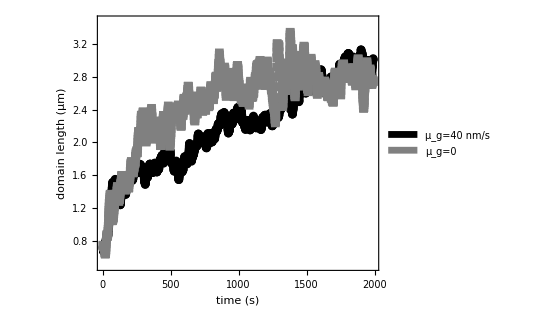

```mathematica
labels={"μ_g=40 nm/s","μ_g=0"};
cols={Black,Gray};
p1=ListPlot[MovingAverage[#,10]&/@{mulen[[5]],mulenNG[[5]]},
FrameLabel->{"time (s)","domain length (μm)"},
PlotLegends->Placed[SwatchLegend[labels,LegendLayout->"Column",Spacings->0],{0.3,0.85}],PlotStyle->cols,PlotRange->{0.5,3.48}]
```

```mathematica
Export[figdir<>"/dx100_difft_mug_time.eps",p1];
```

#### varying lp

afines growing

```mathematica
job="lp_lgrow0.040";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1_wl1999/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs[[2;;]]},{dom,1,2}];
lens=Map[importCheck[#]&,datfs,{2}];
lensf = Map[Flatten,Flatten[lens,{{1},{4},{2,3}}],{2}];
mulen=Map[Mean,lensf,{2}];
(*errlen = Map[StandardDeviation[#]/Sqrt[Length[#]]&,lensf,{2}];*)
```

afines non-growing

```mathematica
job="lkb_grow0_s2dens0.25_ldiff0.100";
topdir=headdir<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1_wl1999/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs[[2;;]]},{dom,1,2}];
lens=Map[importCheck[#]&,datfs,{2}];
lensf = Map[Flatten,Flatten[lens,{{1},{4},{2,3}}],{2}];
mulenNG=Map[Mean,lensf,{2}];
(*errlenNG = Map[StandardDeviation[#]/Sqrt[Length[#]]&,lensf,{2}];*)
```

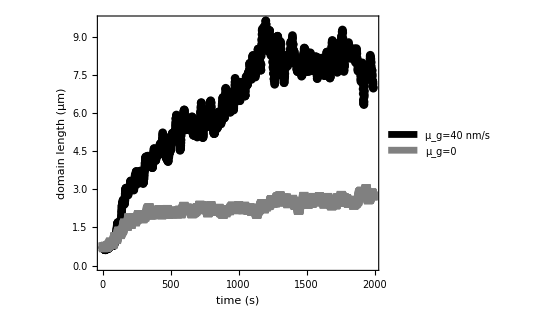

```mathematica
labels={"μ_g=40 nm/s","μ_g=0"};
cols={Black,Gray};
p1=ListPlot[MovingAverage[#,10]&/@{mulen[[4]],mulenNG[[4]]},
FrameLabel->{"time (s)","domain length (μm)"},
PlotLegends->Placed[SwatchLegend[labels,LegendLayout->"Column",Spacings->0],{0.3,0.85}],PlotStyle->cols,PlotRange->Full]
```

```mathematica
Export[figdir<>"/lp17_difft_mug_time.eps",p1];
```

### lgrow = 0, kbend varying

```mathematica
kb0s={"0.004", "0.01", "0.02", "0.04", "0.08", "0.1", "0.2", "0.4"};
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="kbend_s2len0.3_kexv0_kbrat1_nc";
topdir=headdir<>"/"<>job;
ti=1000;
angThresh=0.8;
winlen=100;
s1dens="0.250";

avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

```mathematica
ParallelDo[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/kb0",kb0}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"kb0",kb0,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{kb0,kb0s}
];
```

#### importing

```mathematica
jobs={"kbend","kbend_s2len0.25_kon2_s1init","kbend_s2len0.227_kon2_s1init","kbend_s2len0.227_kon4_s1init","kbend_s2len0.227_kon8_s1init"};
jobs={"kbend","kbend_s2len0.3_kon2_nc","kbend_s2len0.3_kexv0_nc","kbend_s2len0.3_kexv0_kbrat1_nc","kbend_s2len0.3_kon2_nc_kboverlen"};
(*jobs={"kbend","kbend_s2len0.3_kon2_kexv0","kbend_s2len0.227_kon4","kbend_s2len0.227_kon4_kexv0"};
jobs={"kbend","kbend_s2len0.2_s1len0.3"};*)
topdirs=headdir<>"/"<>#&/@jobs;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1000_wl100/kb0",kb0,"_doms",dom,".dat"}],{topdir,topdirs},{kb0,kb0s},{dom,1,2}];
```

```mathematica
lens=Map[importCheck[#]&,datfs,{3}];
```

```mathematica
(*lensf = Map[Flatten,Flatten[lens,{{1},{2},{5},{3,4}}],{3}];
mulenNG=Map[Mean,lensf,{3}];
ListPlot[MovingAverage[#,10]&/@mulenNG,PlotMarkers->None,PlotRange->Full]*)
```

```mathematica
ti1000=Map[Flatten,lens,{4}];
musperseed = Map[meanorzero,ti1000,{4}];
musperdom = Map[Mean,musperseed,{3}];
errperdom=Map[errorzero,musperseed,{3}];
mudom=Map[Mean,musperdom,{2}];
```

```mathematica
errdom=Table[mudom[[i]]*Sqrt[(errperdom[[i,All,1]]/musperdom[[i,All,1]])^2+(errperdom[[i,All,2]]/musperdom[[i,All,2]])^2],{i,Length[mudom]}];
```

```mathematica
(*ti1000lens = Table[Flatten@lensf[[i,1000;;1099]],{i,Length[lensf]}];
mulens =Mean/@ti1000lens;
errlens=(StandardDeviation[#]/Sqrt[Length[#]]) &/@ti1000lens;*)
```

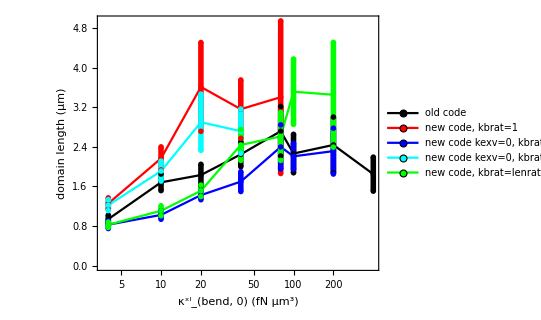

```mathematica
domlens=Table[errcurves[1000*(ToExpression/@(kb0s)),mudom[[i]],errdom[[i]]],{i,Length[mudom]}];
curves=Flatten[domlens,1];
cols={Black,Red,Blue,Cyan,Green,Orange};
pms=Flatten[Table[errbarpms[col,Disk[],0.04],{col,cols}],1];
labels={"old code","new code, kbrat=1","new code kexv=0, kbrat=lenrat","new code kexv=0, kbrat=1","new code, kbrat=lenrat"};
(*labels={"s1=200, s2=300","s1=300, s2=200",(*"dx=50","dx=50, s1init",*)"dx=27","dx=27, s1init"};*)
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->Full(*{Automatic,{0.8,4.5}}*),
FrameLabel->{"(κ^xl)_(bend, 0) (fN μm^3)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0],Right]]
```

```mathematica
Export[figdir<>"/mar19/kbend_varying_codes.eps",p1];
```

```mathematica
kb0s
```

{0.004,0.01,0.02,0.04,0.08,0.1,0.2,0.4}

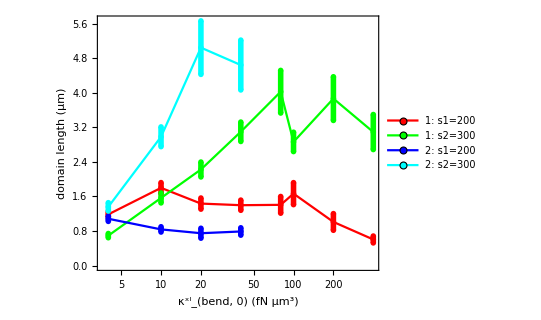

```mathematica
domlens=Table[errcurves[1000*(ToExpression/@(kb0s)),musperdom[[i,All,d]],errperdom[[i,All,d]]],{i,{1,4}},{d,1,2}];
curves=Flatten[domlens,2];
cols={Red,Green,Blue,Cyan};
pms=Flatten[Table[errbarpms[col,Disk[],0.04],{col,cols}],1];
labels={"1: s1=200","1: s2=300","2: s1=200","2: s2=300"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->Full(*{Automatic,{0.8,4.5}}*),
FrameLabel->{"(κ^xl)_(bend, 0) (fN μm^3)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0],Right]]
```

```mathematica
Export[figdir<>"/mar19/kbend_long_vs_short_dx100and50_nc.eps",p1];
```

### lgrow = 0, kl varying

```mathematica
kls={"0.1", "0.2", "0.5", "1","2","5","10","20","50"};
seeds=Range[20];
s1dens="0.250";
s2dens="0.25";
```

#### averaging over seeds

afines

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
job="kl_s2len0.3_kb00.02";
topdir=headdir<>"/"<>job;
ti=1000;
angThresh=0.8;
winlen=100;
s1dens="0.250";

avgdldir=topdir<>"/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
t100dir=topdir<>"/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen];
CreateDirectory[avgdldir];
CreateDirectory[t100dir];
```

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.02/dom_lens/avg_err_ns_ti1000_wl100 already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.02/dom_lens/ti1000_wl100 already exists.

```mathematica
ParallelDo[
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/kl",kl}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"kl",kl,"_doms",dom,".dat"}];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=t100dir<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=avgdldir<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{kl,kls}
];
```

#### importing

```mathematica
jobs={"kbend","kbend_s2len0.25_kon2_s1init","kbend_s2len0.227_kon2_s1init","kbend_s2len0.227_kon4_s1init","kbend_s2len0.227_kon8_s1init"};
jobs={"kl_s2len0.3_kb00.02","kl_s2len0.3_kb00.1"};
(*jobs={"kbend","kbend_s2len0.3_kon2_kexv0","kbend_s2len0.227_kon4","kbend_s2len0.227_kon4_kexv0"};
jobs={"kbend","kbend_s2len0.2_s1len0.3"};*)
topdirs=headdir<>"/"<>#&/@jobs;
datfs=Table[StringJoin[ToString/@{topdir,"/dom_lens/ti1000_wl100/kl",kl,"_doms",dom,".dat"}],{topdir,topdirs},{kl,kls},{dom,1,2}];
```

```mathematica
lens=Map[importCheck[#]&,datfs,{3}];
```

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.02/dom_lens/ti1000_wl100/kl50_doms1.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.02/dom_lens/ti1000_wl100/kl50_doms2.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl10_doms1.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl10_doms2.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl20_doms1.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl20_doms2.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl50_doms1.dat doesn't exist or is empty

/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kl_s2len0.3_kb00.1/dom_lens/ti1000_wl100/kl50_doms2.dat doesn't exist or is empty

```mathematica
(*lensf = Map[Flatten,Flatten[lens,{{1},{2},{5},{3,4}}],{3}];
mulenNG=Map[Mean,lensf,{3}];
ListPlot[MovingAverage[#,10]&/@mulenNG,PlotMarkers->None,PlotRange->Full]*)
```

```mathematica
ti1000=Map[Flatten,lens,{4}];
musperseed = Map[meanorzero,ti1000,{4}];
musperdom = Map[Mean,musperseed,{3}];
errperdom=Map[errorzero,musperseed,{3}];
mudom=Map[Mean,musperdom,{2}];
```

```mathematica
errdom=Table[mudom[[i]]*Sqrt[(errperdom[[i,All,1]]/musperdom[[i,All,1]])^2+(errperdom[[i,All,2]]/musperdom[[i,All,2]])^2],{i,Length[mudom]}];
```

```mathematica
(*ti1000lens = Table[Flatten@lensf[[i,1000;;1099]],{i,Length[lensf]}];
mulens =Mean/@ti1000lens;
errlens=(StandardDeviation[#]/Sqrt[Length[#]]) &/@ti1000lens;*)
```

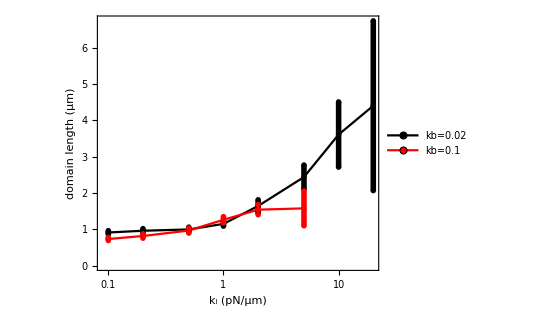

```mathematica
domlens=Table[errcurves[(ToExpression/@(kls)),mudom[[i]],errdom[[i]]],{i,Length[mudom]}];
curves=Flatten[domlens,1];
cols={Black,Red,Blue,Cyan,Green,Orange};
pms=Flatten[Table[errbarpms[col,Disk[],0.04],{col,cols}],1];
labels={"kb=0.02","kb=0.1"};
(*labels={"s1=200, s2=300","s1=300, s2=200",(*"dx=50","dx=50, s1init",*)"dx=27","dx=27, s1init"};*)
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->Full(*{Automatic,{0.8,4.5}}*),
FrameLabel->{"k_l (pN/μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0],Right]]
```

```mathematica
Export[figdir<>"/mar19/kl_varying_kbs.eps",p1];
```

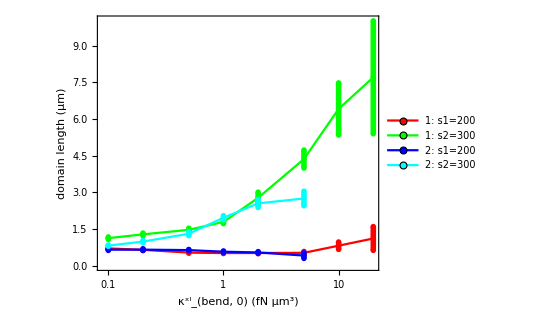

```mathematica
domlens=Table[errcurves[(ToExpression/@(kls)),musperdom[[i,All,d]],errperdom[[i,All,d]]],{i,{1,2}},{d,1,2}];
curves=Flatten[domlens,2];
cols={Red,Green,Blue,Cyan};
pms=Flatten[Table[errbarpms[col,Disk[],0.04],{col,cols}],1];
labels={"1: s1=200","1: s2=300","2: s1=200","2: s2=300"};
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->Full(*{Automatic,{0.8,4.5}}*),
FrameLabel->{"(κ^xl)_(bend, 0) (fN μm^3)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0],Right]]
```

```mathematica
Export[figdir<>"/mar19/kl_long_vs_short_kb.eps",p1];
```

## fig 5A-B : growing filaments

### frames

```mathematica
densrats={0.5,1,2};
s2dens="0.25";
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];
seeds={5,4,1};
ts={100,200,400,650};
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/kgrow_diff0.100_maxlinks15_s1koff10.05_s2init/seed",seeds[[i]],"e7/lgrow0.040_s1dens",s1densstrs[[i]]}],{i,Length[seeds]}];
```

```mathematica
links=pts4[#,"links"][[ts]]&/@dirs;
conn1s=pts4[#,"spacers1_bound"][[ts]]&/@dirs;
conn2s=pts4[#,"spacers2_bound"][[ts]]&/@dirs;
```

```mathematica
(*centering filaments and xlinks to middle of frame*)
zeros=Table[Join[links[[i,t,1,1;;2]],{0,0}],{i,Length[links]},{t,Length[links[[i]]]}];
fov={35,20};

lc=Table[Join[rijP[links[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],links[[i,t,l,3;;]]],{i,Length[links]},{t,Length[links[[i]]]},{l,Length[links[[i,t]]]}];
s1c=Table[Join[rijP[conn1s[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],conn1s[[i,t,l,3;;]]],{i,Length[conn1s]},{t,Length[conn1s[[i]]]},{l,Length[conn1s[[i,t]]]}];
s2c=Table[Join[rijP[conn2s[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],conn2s[[i,t,l,3;;]]],{i,Length[conn2s]},{t,Length[conn2s[[i]]]},{l,Length[conn2s[[i,t]]]}];
```

```mathematica
frs=Table[drawmixed[{},links[[i]],conn1s[[i]],conn2s[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan]],{i,Length[links]}];
```

```mathematica
frsc=Table[drawmixed[{},lc[[i]],s1c[[i]],s2c[[i]],"",False,{35,20},True,26,Green,Red,Darker[Cyan],"",White,-1,3,False],{i,Length[links]}];
```

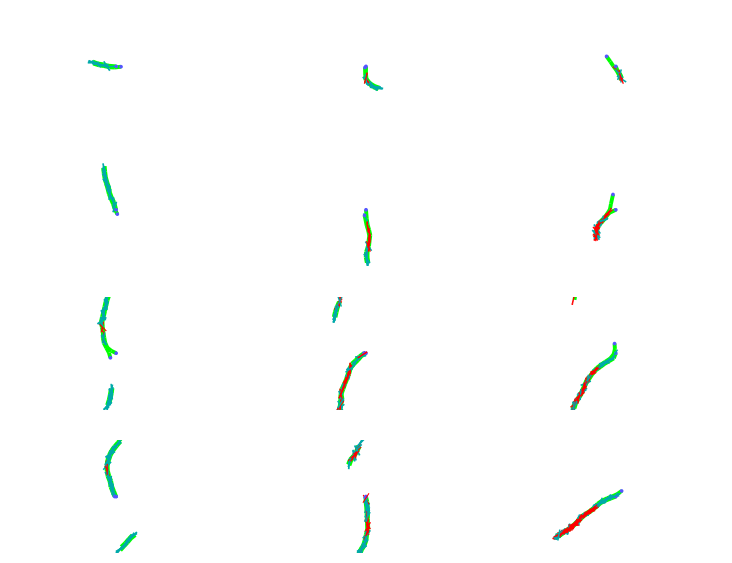

```mathematica
GraphicsGrid[frscᵀ]
```

```mathematica
Do[Export[figdir<>"/diff100_frames/densrat"<>ToString[densrats[[i]]]<>"_t"<>ToString[ts[[j]]]<>"a_noframe.eps",frsc[[i,j]]],{i,Length@densrats},{j,Length@ts}];
```

### averaging over seeds for growing, increasing density ratio

```mathematica
seeds=Range[20];
s2dens="0.25";
densrats={0.2,0.5,1,1.25,1.33,1.5,2,3};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];

inits={"1","2"};
doms={1,2};
domfs="/analysis/spacer"<>ToString[#]<>"_domains_t1-2000_nc4_rc1.dat"&/@doms;
lgrow="0.040";
angThresh=0.8;
winlen=100;
```

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
```

```mathematica
Do[
job="kgrow_diff0.100_maxlinks15_s1koff10.05_s"<>init<>"init";
topdir=headdir<>"/"<>job;
dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/lgrow",lgrow,"_s1dens",dens}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"lgrow",lgrow,"_dens",dens,"_doms",dom,".dat"}];
ti=Ceiling[15/ToExpression@lgrow];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=topdir<>"/dom_lens/t100_window"<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=topdir<>"/dom_lens/avg_err_ns"<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{init,inits},
{dens,s1densstrs}
];
```

### plotting

```mathematica
(*simulation data*)
densrats={0.2,0.5,1,1.25,1.33,1.5,2,3};
(*densrats={0.2,0.3,0.5,0.8,1,1.5,2,3};*)
s2dens="0.25";
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];

datfs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/kgrow_diff0.100_maxlinks15_s1koff10.05_s"<>ToString[init]<>"init/dom_lens/avg_err_ns/lgrow0.040_dens",dens,
"_doms",dom,".dat"}],{init,1,2},{dom,1,2},{dens,s1densstrs}];
dps=Map[importCheck[#][[All,1]]&,datfs,{3}];

avgdps=0.5(dps[[1]]+dps[[2]]);
errscaled=dps[[All,All,All,2]]/dps[[All,All,All,1]];
s1doms=errcurves[densrats,avgdps[[1,All,1]],avgdps[[1,All,1]]*Sqrt[errscaled[[1,1]]^2+errscaled[[2,1]]^2]];
s2doms=errcurves[densrats,avgdps[[2,All,1]],avgdps[[2,All,1]]*Sqrt[errscaled[[1,2]]^2+errscaled[[2,2]]^2]];
```

```mathematica
(*experimental data from winkelman 2016*)
exptDat={{0,0,0},{0.15,0.3,0.1},{0.2,0,0},{0.27,0.3,0.2},{0.3,2.3,1.6},{0.5,1,1.1},{0.6,2.5,0.5},{0.8,1.7,0.7},{1.05,5.8,3.2},{1.3,3.2,1},{1.6,6,2.3}};
exptdoms=errcurves[exptDat[[All,1]],exptDat[[All,2]],exptDat[[All,3]]];
```

```mathematica
(*KMC data*)
theordatf=Import[figdir<>"/kmc_domain_szs.txt","Data"];
t1doms=errcurves[theordatf[[All,1]],theordatf[[All,2]],theordatf[[All,3]]];
t2doms=errcurves[theordatf[[All,1]],theordatf[[All,4]],theordatf[[All,5]]];
t1doms2=Map[#/{1,1000}&,t1doms,{2}];
t2doms2=Map[#/{1,1000}&,t2doms,{2}];
```

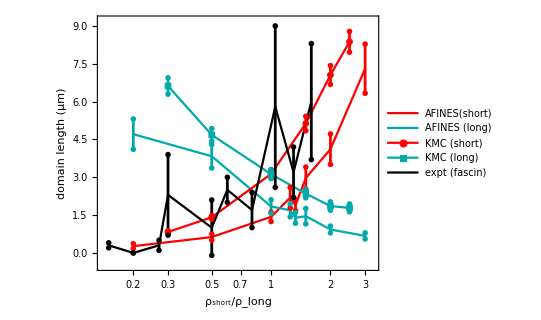

```mathematica
labels={ "AFINES(short)","AFINES (long)","KMC (short)","KMC (long)","expt (fascin)"};
cols={Red,Darker[Cyan],Red,Darker[Cyan],Black};
pms=Join[
errbarpms[cols[[1]],{Transparent,EdgeForm[Directive[Thick,cols[[1]]]],Disk[]}],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}],
errbarpms[cols[[3]],{(*Transparent,*)EdgeForm[Directive[Thick,cols[[3]]]],Disk[]}],
errbarpms[cols[[4]],{(*Transparent,*)EdgeForm[Directive[Thick,cols[[4]]]],Rectangle[]}],
errbarpms[cols[[5]],{Transparent,EdgeForm[Directive[Thick,cols[[5]]]],SSSTriangle[1,1,1]}]
(*{{●,15}}*)
];

fs=Directive[Opacity[1],Thickness[0.005]];

p1=ListLogLinearPlot[Join[s1doms[[All,1;;-1]],s2doms[[All,1;;-1]],t1doms2,t2doms2,exptdoms],
PlotRange->{{0.14,3.3},{-0.5,9.2}},(*{{0.1,1.8},{-0.5,11.8}},*)
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
FrameLabel->{"ρ_short/ρ_long","domain length (μm)"},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotRange->Full,
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],(*{0.45,0.8}*)Right]]
```

## fig 5D-E : bar plots

### koff 1

#### averaging over seeds

```mathematica
koffs={"0.05","0.10","0.15","0.20","0.25","0.30","0.35","0.50"};
lgrows={"0.010","0.100"};
seeds=Range[20];
inits={"1","2"};
s2dens="0.25";
densrats={1,1.5,2};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];
doms={1,2};
domfs="/analysis/spacer"<>ToString[#]<>"_domains_t1-2000_nc4_rc1.dat"&/@doms;

angThresh=0.8;
winlen=100;
```

```mathematica
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
(*todeletedirs=Import["~/Code/cytomod/spacer_metadata/kgrow_kfac/crashed_list.txt","Table"][[All,1]];*)
```

```mathematica
Do[
job="kgrow_diff0.100_maxlinks15_s1koff1"<>koff<>"_s"<>init<>"init";
topdir=headdir<>"/"<>job;

dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/lgrow",lgrow,"_s1dens",dens}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"lgrow",lgrow,"_dens",dens,"_doms",dom,".dat"}];

(*ti=1500;
dirsuf="_ti1500/";*)
ti=Ceiling[15/ToExpression@lgrow];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=topdir<>"/dom_lens/t100_window"<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=topdir<>"/dom_lens/avg_err_ns"<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{koff,koffs},
{init,inits},
{lgrow,lgrows},
{dens,s1densstrs}
];
```

```mathematica
(*todeletedirs1=Import["~/Code/cytomod/spacer_metadata/"<>job<>"/crashed.txt","Table"][[All,1]];*)
```

#### plotting

```mathematica
koffs={"0.05","0.10","0.20","0.50"};
densrats={1,1.5,2};
lgrows={"0.010","0.100"};

s2dens="0.25";
densrats={1,1.5,2};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];

datfs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/",
"kgrow_diff0.100_maxlinks15_s1koff1",koff,
"_s",init,"init",
"/dom_lens_copy/avg_err_ns/lgrow",lg,
(*"/dom_lens/avg_err_ns_ti1500/lgrow",lg,*)
"_dens",dens,
"_doms",dom,".dat"}],{init,1,2},{dom,1,2},{koff,koffs},{lg,lgrows},{dens,s1densstrs}];
```

```mathematica
dps=Map[importCheck[#][[All,1]]&,datfs,{5}];
```

```mathematica
mus=Mean[dps[[All,All,All,All,All,1]]];
errrats=Map[divorzero[#[[2]],#[[1]]]&,dps,{5}];
errs=mus Sqrt[errrats[[1,All,All,All,All]]^2+errrats[[2,All,All,All,All]]^2];
```

```mathematica
w1=3/8;
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=
Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],
{Black,
Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},
{{x0+w1(x1-x0),y1+error},{x1-w1(x1-x0),y1+error}},
{{x0+w1(x1-x0),y1-error},{x1-w1(x1-x0),y1-error}}}]}}]
```

```mathematica
framesettings=
{Frame->{{False,True},{False,False}},FrameTicks->{{None,{{2,"",{0.04,0},Thick},{4,"",{0.04,0},Thick},{6,"",{0.04,0},Thick}}},None},
FrameStyle->Black};
```

```mathematica
(*musf=Flatten@mus;errsf=Flatten@errs;*)
chartData=Table[{
{mus[[1,i,2,j]]->errs[[1,i,2,j]],mus[[2,i,2,j]]->errs[[2,i,2,j]]},
{mus[[1,i,1,j]]->errs[[1,i,1,j]],mus[[2,i,1,j]]->errs[[2,i,1,j]]}}
,{i,Length[koffs]},{j,Length[densrats]}];
t2=Table[BarChart[chartData[[i,j]],ChartElementFunction->errorBar[],
PlotRange->{0,7},Axes->None,Evaluate@framesettings,AspectRatio->0.75,ChartStyle->{{EdgeForm[],EdgeForm[Black]},{Red,Darker[Cyan]}}],{i,Length[koffs]},{j,Length[densrats]}];
```

```mathematica
koffrats=ToExpression@(integerize@(ToExpression/@koffs/0.05));
```

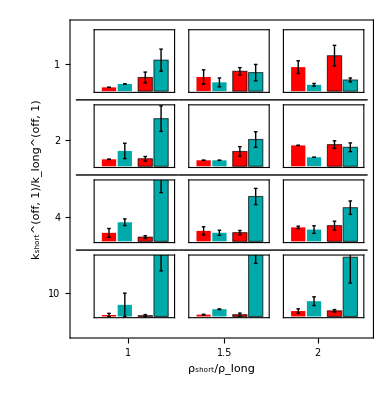

```mathematica
p1=Show[
GraphicsGrid[t2,Frame->All,Spacings->{{60,0,0,0},{0,10,10,10,60}},FrameStyle->White,Dividers->{False,{2->Black,3->Black,4->Black}}],
FrameMargins->100,
Frame->True,
FrameLabel->{"ρ_short/ρ_long","k_short^(off, 1)/k_long^(off, 1)"},FrameStyle->Directive[FontSize->18,Black],
FrameTicks->{{{200,"1"},{565,"1.5"},{920,"2"}},{-140-285Range[0,Length[koffrats]-1],koffrats}ᵀ,None,None}
]
```

```mathematica
Export[outdir<>"/xlink_segregation/figs/paper/koff1_bar_chart_grid_rc.eps",p1];
```

#### movies

```mathematica
koffs={"0.05","0.20"};
lgrows={"0.010","0.100"};
```

```mathematica
(11 is good)
```

```mathematica
idxs={1,2};
```

```mathematica
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/kgrow_diff0.100_maxlinks15_s1koff10.05_s1init/seed6e7/lgrow",lgrow,"_s1dens0.250"}],{lgrow,lgrows}];
```

```mathematica
links=pts4[#,"links"]&/@(dirs[[idxs]]);
conn1s=pts4[#,"spacers1_bound"]&/@(dirs[[idxs]]);
conn2s=pts4[#,"spacers2_bound"]&/@(dirs[[idxs]]);
```

```mathematica
linkz=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];
```

```mathematica
mov=Table[drawmixed[{},linkz[[i]],conn1z[[i]],conn2z[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];
```

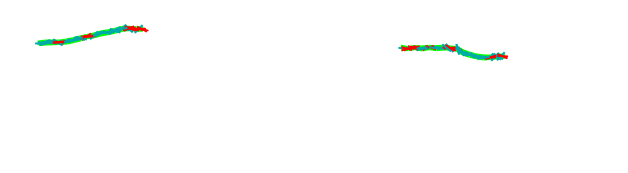

```mathematica
GraphicsRow[{mov[[1,1500]],mov[[2,240]]}]
```

```mathematica
Dimensions[mov]
```

{2,2001}

```mathematica
tfslow=1500;
tffast=240;
mov2stop=Join[mov[[2,1;;tffast]],ConstantArray[mov[[2,tffast]],tfslow-tffast]];
```

```mathematica
Dimensions[mov2stop]
```

{1500}

```mathematica
dimovie=Table[GraphicsRow[{mov[[1,t]],mov[[2,t]]},Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
```

```mathematica
dimovieStop=Table[GraphicsRow[{mov[[1,t]],mov2stop[[t]]},Frame->All,Spacings->0],{t,tfslow}];
```

```mathematica
Export[figdir<>"/lgrows10_100_koff1_s6_100s.avi",dimovieStop];
```

### kfactor

#### averaging over seeds

```mathematica
kfacs={"0.25","0.5",};
lgrows={"0.010","0.100"};
seeds=Range[20];
inits={"1","2"};

s2dens="0.25";
densrats={1,1.5,2};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];

doms={1,2};
domfs="/analysis/spacer"<>ToString[#]<>"_domains_t1-2000_nc4_rc1.dat"&/@doms;

angThresh=0.8;
winlen=100;
todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
```

```mathematica
Do[
job="kgrow_kfac_diff0.100_maxlinks15_s1len0.20_s"<>init<>"init";
topdir=headdir<>"/"<>job;

dirs=Table[StringJoin[ToString/@{topdir,"/seed",sd,"e7/lgrow",lgrow,"_s1dens",dens,"_k2fac",kf}],{sd,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];

fname=StringJoin[ToString/@{"kfac",kf,"_lgrow",lgrow,"_dens",dens,"_doms",dom,".dat"}];

ti=Ceiling[15/ToExpression@lgrow];
dirsuf="/";

angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

outf=topdir<>"/dom_lens/t100_window"<>dirsuf<>fname;
Export[outf,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];
outf=topdir<>"/dom_lens/avg_err_ns"<>dirsuf<>fname;
Export[outf,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{kf,kfacs},
{init,inits},
{lgrow,lgrows},
{dens,s1densstrs}
];
```

#### plotting

```mathematica
kfacs={"0.5","0.25"};
densrats={1,1.5,2};

lgrows={"0.010","0.020","0.030","0.040","0.050","0.070","0.100"(*,"0.200","0.300"*)};
lgrows={"0.010","0.100"};

s2dens="0.25";
densrats={1,1.5,2};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];

datfs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/",
"kgrow_kfac_diff0.100_maxlinks15_s1len0.20",
"_s",init,"init",
"/dom_lens/avg_err_ns/kfac",kf,
"_lgrow",lg,
"_dens",dens,
"_doms",dom,".dat"}],{init,1,2},{dom,1,2},{kf,kfacs},{lg,lgrows},{dens,s1densstrs}];
```

```mathematica
dps=Map[importCheck[#][[All,1]]&,datfs,{5}];
```

```mathematica
mus=Mean[dps[[All,All,All,All,All,1]]];
errrats=Map[divorzero[#[[2]],#[[1]]]&,dps,{5}];
errs=mus Sqrt[errrats[[1,All,All,All,All]]^2+errrats[[2,All,All,All,All]]^2];
```

```mathematica
(*musf=Flatten@mus;errsf=Flatten@errs;*)
chartData=Table[{
{mus[[1,i,2,j]]->errs[[1,i,2,j]],mus[[2,i,2,j]]->errs[[2,i,2,j]]},
{mus[[1,i,1,j]]->errs[[1,i,1,j]],mus[[2,i,1,j]]->errs[[2,i,1,j]]}}
,{i,Length[kfacs]},{j,Length[densrats]}];
t2=Table[BarChart[chartData[[i,j]],ChartElementFunction->errorBar[],
Evaluate@framesettings,
PlotRange->{0,7},Axes->None,AspectRatio->0.75,ChartStyle->{{EdgeForm[],EdgeForm[Black]},{Red,Darker[Cyan]}}],{i,Length[kfacs]},{j,Length[densrats]}];
```

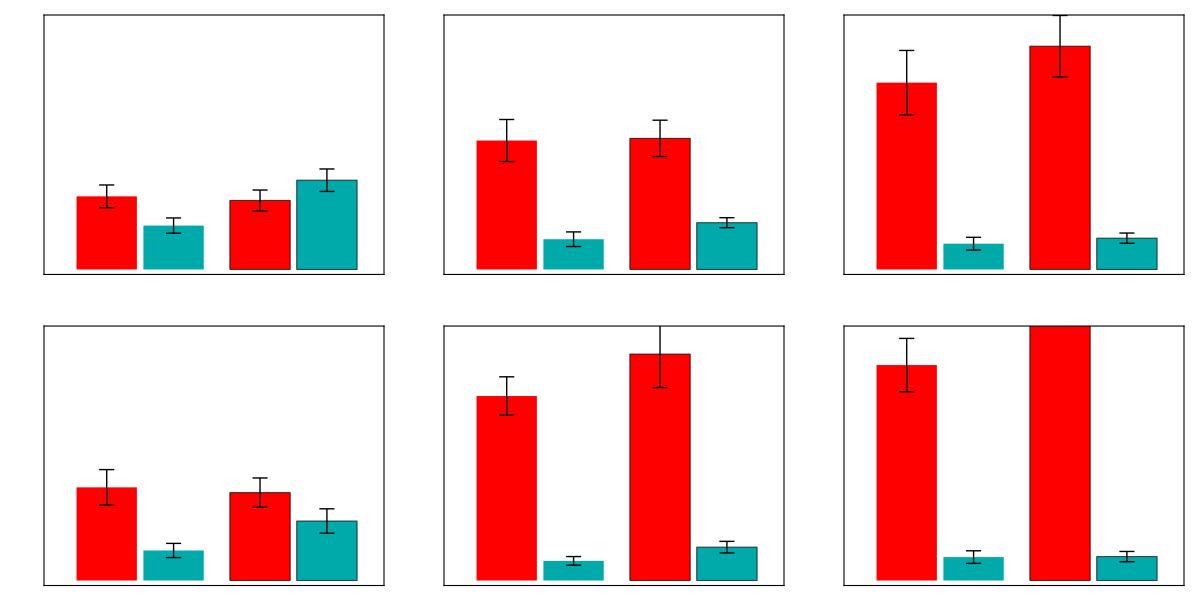

```mathematica
p1=Show[
GraphicsGrid[t2,Frame->{False,True},Spacings->{{60,0,0},{0,10,60}},FrameStyle->White,Dividers->{False,{2->Black}}](*Scaled[0.1]]*),
Frame->True,FrameLabel->{"ρ_short/ρ_long","k_short^(on, off)/k_long^(on, off)"},FrameStyle->Directive[FontSize->18,Black],
FrameTicks->{{{200,"1"},{565,"1.5"},{920,"2"}},{{-140,2},{-400,4},{-750,4},{-1025,0.5},{-1300,0.25}},None,None}
]
```

```mathematica
Export[outdir<>"/xlink_segregation/figs/paper/kfac_bar_chart_grid_rc.eps",p1];
```

#### movies

```mathematica
lgrows={"0.010","0.100"};
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/kgrow_kfac_diff0.100_maxlinks15_s1len0.20_s1init/seed1e7/lgrow",lgrow,"_s1dens0.250_k2fac2"}],{lgrow,lgrows}];
```

```mathematica
idxs={1,2};
```

```mathematica
links=pts4[#,"links"]&/@(dirs[[idxs]]);
conn1s=pts4[#,"spacers1_bound"]&/@(dirs[[idxs]]);
conn2s=pts4[#,"spacers2_bound"]&/@(dirs[[idxs]]);
```

```mathematica
linkz=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];
```

```mathematica
mov=Table[drawmixed[{},linkz[[i]],conn1z[[i]],conn2z[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];
```

```mathematica
trimovie=Table[GraphicsRow[{mov[[1,t]],mov[[2,t]]},Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
```

```mathematica
Export[figdir<>"/lgrows10_100_kfac2.avi",trimovie];
```

```mathematica
Export[figdir<>"/lgrows10_100_kfac2.tiff",trimovie];
```

## testing domain calculation

### calculation steps

```mathematica
fidx=0;
dir=outdir<>"/xlink_segregation/spacers/denstot_0.5_s2init/seed3e7/lgrow0_s1dens0.250";
t=500;
fov={35,20};
lmax=15;
l0=0.037;
```

```mathematica
lks=pts4[dir,"links"];
flks=Map[Cases[#,_?((#[[5]]==fidx)&)]&,lks];
conn1s=pts4[dir,"spacers1_bound"];
conn2s=pts4[dir,"spacers2_bound"];
```

```mathematica
d1=Table[distFromBarbedEnd[flks[[t]],fidx,conn1s[[t,i]],fov],{i,Length[conn1s[[t]]]}];
d2=Table[distFromBarbedEnd[flks[[t]],fidx,conn2s[[t,i]],fov],{i,Length[conn2s[[t]]]}];
bcs1=BinCounts[d1,{0,lmax,l0}];
bcs2=BinCounts[d2,{0,lmax,l0}];
lattice=Sign[bcs1-bcs2]/.{-1->2};
pos1=Flatten[Position[lattice,1]];
pos2=Flatten[Position[lattice,2]];
```

```mathematica
dom1s=Map[ToExpression,importCheck[dir<>domfs[[1]]],{3}];
dom2s=Map[ToExpression,importCheck[dir<>domfs[[2]]],{3}];
```

```mathematica
xs=(Range[Length[bcs1]]-1)*l0;
dom1st=dom1s[[t,1]];
dom2st=dom2s[[t,1]];
n1=Length[dom1st];
n2=Length[dom2st];
```

```mathematica
Union[bcs2]
```

{0,1,2}

```mathematica
p1=ListPlot[Join[{{xs,bcs1}ᵀ,{xs,bcs2+5}ᵀ,
constFun[(pos1-1)*l0,10.75],constFun[(pos2-1)*l0,10.75]},
Table[constFun[dom1st[[i,{1,-1}]],12],{i,Length[dom1st]}],
Table[constFun[dom2st[[i,{1,-1}]],12],{i,Length[dom2st]}]],
Joined->Join[{True,True,False,False},ConstantArray[True,n1+n2]],
PlotStyle->Join[cols,cols,ConstantArray[Directive[cols[[1]],Thickness[0.01]],n1],ConstantArray[Directive[cols[[2]],Thickness[0.01]],n2]],
PlotMarkers->Join[
{Null,Null,{vline[0.05],0.07},{vline[0.05],0.07}},ConstantArray[{vline[0.5],0.05},n1+n2]
],
FrameLabel->{"position (μm)","number of xlinks\t"},
FrameTicks->{{{{0,c1@0},{1,""},{2,c1@2},{3,""},{4,c1@4},{5,c2@0},{6,""},{7,c2@2},{8,""},{9,c2@4},{10,""}},Join[constFun[Range[10],""],{{10.75,"label",0},{12,"domain",0}}]},Automatic},ImageSize->450]
```

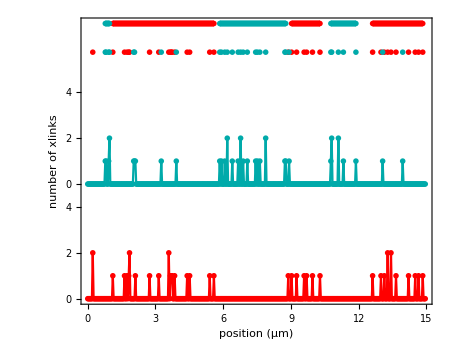

```mathematica
p1=ListPlot[Join[{{xs,bcs1}ᵀ,{xs,bcs2+5}ᵀ,
constFun[(pos1-1)*l0,10.75],constFun[(pos2-1)*l0,10.75]},
Table[constFun[dom1st[[i,{1,-1}]],12],{i,Length[dom1st]}],
Table[constFun[dom2st[[i,{1,-1}]],12],{i,Length[dom2st]}]],
Joined->Join[{True,True,False,False},ConstantArray[True,n1+n2]],
PlotStyle->Join[cols,cols,ConstantArray[Directive[cols[[1]],Thickness[0.01]],n1],ConstantArray[Directive[cols[[2]],Thickness[0.01]],n2]],
PlotMarkers->Join[
{Null,Null,{vline[0.05],0.07},{vline[0.05],0.07}},ConstantArray[{vline[0.5],0.05},n1+n2]
],
FrameLabel->{"position (μm)","number of xlinks\t"},
FrameTicks->{{{{0,c1@0},{1,""},{2,c1@2},{3,""},{4,c1@4},{5,c2@0},{6,""},{7,c2@2},{8,""},{9,c2@4},{10,""}},Join[constFun[Range[10],""],{{10.75,"label",0},{12,"domain",0}}]},Automatic},ImageSize->450]
```

```mathematica
Export[figdir<>"/domain_testing.eps",p1];
```